```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
mub={0,100,200,300,400,450,500,530};
fitdata=Table[Import["./mub"<>ToString[mub[[i]]]<>".dat"],{i,1,Length[mub]}];
```

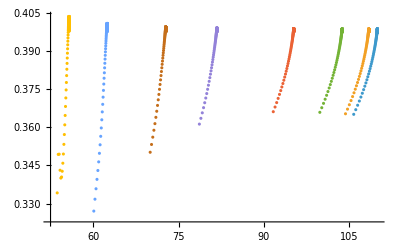

```mathematica
ListPlot[fitdata,PlotRange->All]
```

```mathematica
fitfun=Table[Interpolation[fitdata[[i]]],{i,1,Length[mub]}];
```

```mathematica
T0p39=Table[Flatten[FindRoot[fitfun[[i]][x]-0.39==0,{x,fitdata[[i]][[-1]][[1]],fitdata[[i]][[-1]][[1]],fitdata[[i]][[1]][[1]]}],2][[1]][[2]],{i,1,Length[mub]}]
Export["beta0p39.dat",%];
```

FindRoot::reged: 点 {72.7655} 位于搜索区域 {70.0005,72.7655} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

FindRoot::reged: 点 {62.4464} 位于搜索区域 {60.0735,62.4464} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

FindRoot::reged: 点 {55.7494} 位于搜索区域 {53.6309,55.7494} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

General::stop: 在本次计算中，FindRoot::reged 的进一步输出将被抑制.

{109.433,107.929,103.231,94.7198,81.258,72.7655,62.4464,55.7494}

```mathematica
T0p38=Table[Flatten[FindRoot[fitfun[[i]][x]-0.38==0,{x,fitdata[[i]][[-3]][[1]],fitdata[[i]][[-1]][[1]],fitdata[[i]][[1]][[1]]}],2][[1]][[2]],{i,1,Length[mub]}]
Export["beta0p38.dat",%];
```

FindRoot::reged: 点 {62.4464} 位于搜索区域 {60.0735,62.4464} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

FindRoot::reged: 点 {55.7494} 位于搜索区域 {53.6309,55.7494} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

{108.346,106.845,102.164,93.724,80.5503,71.8949,62.4464,55.7494}

```mathematica
T0p37=Table[Flatten[FindRoot[fitfun[[i]][x]-0.37==0,{x,fitdata[[i]][[-1]][[1]],fitdata[[i]][[-1]][[1]],fitdata[[i]][[1]][[1]]}],2][[1]][[2]],{i,1,Length[mub]}]
Export["beta0p37.dat",%];
```

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法使优化目标函数的值减小得足够多. 您可能需要多于 MachinePrecision 位的工作精度以满足这些容差.

{106.78,105.285,100.635,92.3268,79.6427,71.3774,61.6664,53.894}

```mathematica
Export["mub.dat",mub]
```

mub.dat

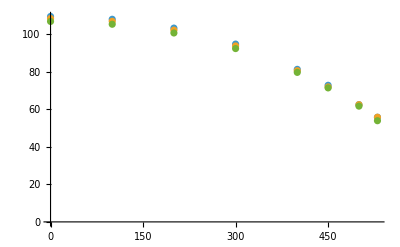

```mathematica
ListPlot[{Transpose[{mub,T0p39}],Transpose[{mub,T0p38}],Transpose[{mub,T0p37}]}]
```